```mathematica
SetDirectory[NotebookDirectory[]]
f[t_]:=Log[2t]/(9-t)+Cos[4t]/(Exp[t]+1);
```

/home/kidinnu/Yandex.Disk/University/Disciplines/matlab/ODE-OrbitalMotion

0.338647+(0.213898+(-0.0559487+(0.148781+(-0.366456+(-0.563589+0.504152 (-1.66667+t)) (-1.33333+t)) (-2.66667+t)) (-2.+t)) (-1.+t)) (-3.+t)

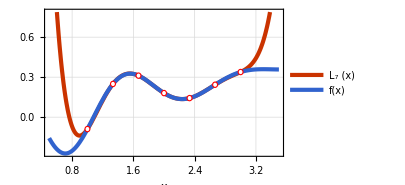

PolyInterpolation.png

```mathematica
t1=1;
t2=3;
data1=Table[{t,f[t]},{t,t1,t2,(t2-t1)/6.0}];
n1=Length[data1];
InterpolatingPolynomial[data1,t]
Plot[{Legended[%,Subscript[L, n1]"(x)"],Legended[f[t],"f(x)"]},{t,t1-0.5,t2+0.5},Epilog->{EdgeForm[Directive[Red]],White,Disk[#,{0.04,0.025}0.8]&/@data1},PlotTheme->{"FrameGrid","Web"},BaseStyle->{10,FontFamily->"Fira Sans"},FrameLabel->{"x"},ImageSize->300]
Export["PolyInterpolation.png",%,ImageResolution->300,Background->None]
```

0.338647+(0.213898+(0.0596387+0.524931 (-2.33333+t)) (-1.+t)) (-3.+t)

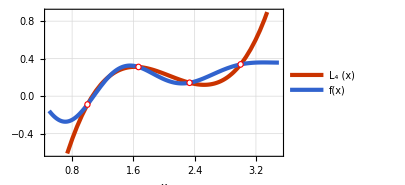

PolyInterpolation2.png

```mathematica
t1=1;
t2=3;
data2=Table[{t,f[t]},{t,t1,t2,(t2-t1)/3.0}];
n2=Length[data2];
InterpolatingPolynomial[data2,t]
Plot[{Legended[%,Subscript[L, n2]"(x)"],Legended[f[t],"f(x)"]},{t,t1-0.5,t2+0.5},Epilog->{EdgeForm[Directive[Red]],White,Disk[#,{0.04,0.035}0.85]&/@data2},PlotTheme->{"FrameGrid","Web"},BaseStyle->{10,FontFamily->"Fira Sans"},FrameLabel->{"x"},ImageSize->300]
Export["PolyInterpolation2.png",%,ImageResolution->300,Background->None]
```

0.338647+(0.157949+(0.406401-0.643144 (-2.33333+t)) (-2.+t)) (-3.+t)

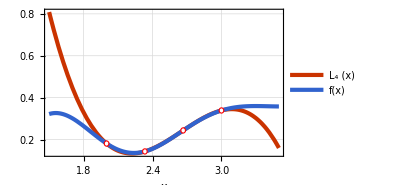

PolyInterpolation3.png

```mathematica
t1=2;
t2=3;
data2=Table[{t,f[t]},{t,t1,t2,(t2-t1)/3.0}];
n2=Length[data2];
InterpolatingPolynomial[data2,t]
Plot[{Legended[%,Subscript[L, n2]"(x)"],Legended[f[t],"f(x)"]},{t,t1-0.5,t2+0.5},Epilog->{EdgeForm[Directive[Red]],White,Disk[#,{0.04,0.025}0.5]&/@data2},PlotTheme->{"FrameGrid","Web"},BaseStyle->{10,FontFamily->"Fira Sans"},FrameLabel->{"x"},ImageSize->300]
Export["PolyInterpolation3.png",%,ImageResolution->300,Background->None]
```

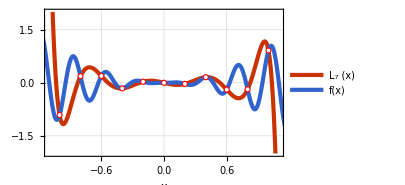

PolyInterpolationBad.png

```mathematica
f[t_]:=Sin[20t] t^2;
t1=-1;
t2=1;
data1=Table[{t,f[t]},{t,t1,t2,(t2-t1)/10}];
n1=Length[data1];
InterpolatingPolynomial[data1,t];
Plot[{Legended[%,Subscript[L, n]"(x)"],Legended[f[t],"f(x)"]},{t,t1-0.5,t2+0.5},Epilog->{EdgeForm[Directive[Red]],White,Disk[#,{0.04,0.12}0.6]&/@data1},PlotTheme->{"FrameGrid","Web"},BaseStyle->{10},FrameLabel->{"x"},ImageSize->300,PlotRange->{{-1.1,1.1},{-2,2}}]
Export["PolyInterpolationBad.png",%,ImageResolution->300,Background->None]
```

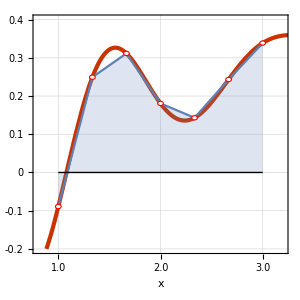

Simpson.pdf

```mathematica
Interpolation[data1,InterpolationOrder->1];
Plot[%[t],{t,t1,t2},Filling->Axis];
Plot[f[t],{t,t1-0.5,t2+0.5},Epilog->{EdgeForm[Directive[Red]],White,Disk[#,{0.04,0.008}0.7]&/@data1,Black,Line[{{1,0},{3,0}}]},PlotTheme->{"FrameGrid","Web"},BaseStyle->{10},FrameLabel->{"x"},ImageSize->300,PlotRange->{{0.8,3.2},{-0.2,0.4}}];
Show[%,%%,AspectRatio->1.0]
Export["Simpson.pdf",%,ImageResolution->600,Background->None]
```